```mathematica
Timing[ CalcGoodForTuple2[{7,11,13,17},10^10000,10^20000]]
```

{61966.1,Null}

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-2584.8526141231280431281273743582877349133361350852 215867
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-2188.2731322990469223903601644184987696416304166029 6819
```

```mathematica
Calculating good values d:\triangle\DataSrc\7\11\13\17\SolutionsBis.txt.140 found.-1286.7259569959945872106278775609496378179957652599 553250
```

```mathematica
CalcGoodForTuple2[{7,11,13,19},0,10^10000]
```

Aborted at value :

$Aborted

```mathematica
Sort[Select[Table[{N[magicGraham[tuple]],tuple},{tuple,Subsets[Prime[Range[2,50]],{5}]}],Abs[#[[1]]]<0.00001&]]
```

{{-9.95526×10^-6,{5,13,71,113,149}},{-9.01813×10^-6,{7,23,29,43,191}},{-7.96752×10^-6,{3,43,47,103,193}},{-7.76476×10^-6,{13,17,29,31,109}},{-6.92399×10^-6,{5,23,31,79,229}},{-6.6313×10^-6,{5,11,73,149,167}},{-6.00905×10^-6,{5,7,163,173,229}},{-4.91707×10^-6,{7,13,47,71,149}},{-4.29004×10^-6,{3,31,61,137,167}},{-3.63485×10^-6,{3,23,71,173,193}},{-2.76713×10^-6,{3,41,61,97,151}},{-9.81418×10^-7,{5,13,71,89,199}},{-3.28657×10^-7,{5,19,47,71,193}},{-1.99388×10^-7,{3,37,59,127,139}},{2.08745×10^-7,{3,31,43,173,229}},{2.31472×10^-6,{3,41,47,139,149}},{2.65038×10^-6,{3,17,131,157,199}},{2.67394×10^-6,{3,19,103,151,211}},{3.22613×10^-6,{3,47,53,103,139}},{3.56496×10^-6,{5,7,167,173,223}},{4.42201×10^-6,{11,17,19,53,163}},{4.56073×10^-6,{3,41,59,101,151}},{4.58309×10^-6,{5,23,43,61,181}},{4.82558×10^-6,{7,29,31,53,83}},{5.10254×10^-6,{5,19,61,83,109}},{5.32602×10^-6,{17,19,23,41,53}},{6.12758×10^-6,{3,43,61,67,229}},{6.51331×10^-6,{5,19,29,127,223}},{6.78172×10^-6,{3,43,61,103,131}},{7.17044×10^-6,{3,43,59,103,137}},{7.35597×10^-6,{3,19,101,163,199}},{7.38258×10^-6,{3,47,53,79,193}},{7.5366×10^-6,{7,13,37,103,139}},{7.66926×10^-6,{5,29,31,73,157}},{8.32783×10^-6,{5,7,139,211,223}},{8.69403×10^-6,{3,31,83,113,137}}}

```mathematica
Timing[ CalcGoodForTuple2[{3,37,59,127,139},42246199943839142615722274391059474047897038086680444081349909369297278748874541329297247015876574013603265500109860516333083352966172614824805881849841689882353380193404233845471549049135819092238478551125860498789699127201848111555308723235512156166038454378779997893448383509742276144907874656319903034383919798720878857858092023509401993477227197535372969262611464366019389903795296411646145138337892909319489302680699381604100104895431554895770128846464327694789630612129553209368970450083104022524384062512485415551995082606700846699097415998993096898863396971324876679286047783419518591709666725929402791285688722938484512838835101858144340482161033154391300173753599878640742414083230301652896676990713240835308981696039786850965138906433011985574967808339209950578983956362635444619796380067546409971255086129979091251404283740522566454377634654809571334491995597095853629166247431559071011284714899333460661508219505779200154584934182189656110453710930750926935392237291873043821134513802317544171349448519312154817024887230197352390601693038015136412143693744511964268200989323645592122795266946665494549164635605204323339679743880105753758804879418572955139660119467123747977045971662992852552674266877130846224364947107047082938375400432909760977937132485977713118303673648167069059084188712459411304899087710594264913394583229329017353754083356619386382976627573804883316556115773872882351974215099742727308199071150114685252928731395111205995191541651681149026135316624699840406033841693941282571483793005490871985334978634261706454708759945515152947578422206298316810136350124642220395015184744474537816972550718735948313319651358524495965203741051404356503645218251639197749632298057321601790479551462288642127080462076269453423142854932491589082984900233605116371948572183834119362193205895790650651354897367989957542978694621593749339407423520125564746479915208760098676658064698815579994891136653296043506755051844617463495458488745521372096486437745505893787339319762482751559662718900720617871608514350466133265065336938137280530190323417740487858492897053974536441338495840824842015001175469346402993944949315471869622038480278375938836080646620632123037290884952613237475598422445093729828941630975342655134801109488418067760843562212963004239522652858279453982792833838800310367222104591897107354867993629478888501620660000260835269531736158656051673853737044789597798097981236818662198018520739291370008012642877572823544733818314007854361209090264695875320082410489576991300395094219276021894687987625720242648300353295030344921943009687501674896305465540522072709007075984573054870343631959339736531981097464590684205278341715890527634460235512168935632920197947632829988617551006976466979615301211851609982368990158443810214625511971447364258627646024113699313460730798533477471625998087395284609141401103910800104911292493758506347873764918722044786225672387410316719573822746296497400349759081220284549880350793838773677450667530299103140838751584684015746661447876988766204078698817811026576166557245075551497496354451024783495986039177243333932127505852837945333069796140780953174346257769625539719437370800532251678659838253896427659204218804428112253083454433194538624644679558767410560315994086850220841829168968707634281231272241871390694447393639092347759964031786787306871348534207374637560356227967251000195367042086319043954741942667299041700298465057184788733613231354955553655947897897228425935319720297161300893678920790586395522117315808983786404885014655018941631960588442144414370475004859971684673799368752660583279375467429479376771390391770240457022034176016319255165934861734800053556288651409786067845621709018384153759321726579829747637336573193833198471793665702650715575830289783876828572886410703021142251132609383683550323142389485452762915073615172605418312852445720905042370405056112285825508938998708965861116248472804845686408507659414092173395141258166927279440462205045425557358457251455897675423639792498163102313278148881751395324057584226475915781540996120731519541740329648709398659839407377104971512756094012052387759820352713380651217668336697640210892749654794214798777275585760631355462933729032398308820954649605221219821485927388028717446529408200195631074526999752639175184743505940208224740937145493580748457528540695908587135491003728635041238881522194737043064048025682141206719436660230282128925733932792603678194512354825507509836964331121007929835613050703175202664212176984151639089319740188534292376598671544934322346540033547221977026967246432783356977071890253689670356366480506786928716772540160244939824044533713489749809470389757967751963700977103546023289537506913223709519291785950166230853414514636292466357608790330488858459816039802954682435570254181804344412740448433161966352063941689152312583171461765319735014678443357146222312062367307080502895861264114751703339047386839551504247959550943655302444307277238186997327527132041971910124553586857430446236892565812887757869402777878708905613388813206715660675788652461545889555304836866401896397170360354452480327870452196806445358055759023357117238290469490559037084263334901460090729373650065563914070452919116963291034042256275161012186893538376879738586875618689076386362018791888398502050200990939474267057405941241537066260316875757116276224126147579069034952063051370886052746252161600073304576606611908916326624696733784558002954663203466825145078829361822651760197004332429021106394484723635109401599784164835215934124769755166592566556875008276272282444937003132587248462360592313221743520950954149035847589627434502314306746420887437963564923153339640861660614424426896854654382725869640294531978031942795383243851884617883739255466694478791559485620479439907720015018257490831326672607782044142241846547009738247568232162403075111862298717798815365256488295323889505898346082481029939974948861562986104613278040680121308485897411384002680885275961936253221428031219093763490582267626782331331731392308356945683424872679922631243039684677529261447327247297255207054765277653416677990635239439274858835673597080603642959104917873748158105313196105433824000731738976314231650451397788925071359448914467918297453536532131457026921369812462907730909068783289746506419294996813086678000797480258706190109850057568100545596264177778123094806878136544396498403949760639991728093208409624975447103465822762085241933867856370255362836691638305848955250827764002306828173362719442204148025797136119372022298471692093895997650016126355620626371705018489562009252777315532578585035545155043537613160867529462860333865060693779473999647336045985005441097561272045361442435479215942078496837516697136101611012850892693519674171632071268980219030697612982404837133080851278537485613755426068093519076331110108850272269050340326090473255523107326387272557979743625646334789890600364870913289959523848831587563489865553934040260324982935700044,10^20000]]
```

Aborted at value :

{43209.5,Null}

Aborted at value :

Aborted at value :

{4348.81,Null}

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-14421.126117495917387228329301201963839515874999418 4364725 (8404.11)-8513.11-(14416.2)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 1314232 (8643.29)-11160.3-(11344.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 745366 (8797.1)-9154.34-(10794.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 1516482 (2626.29)-2772.87-(9432.78)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 1468865 (2693.89)-2977.7-(9432.78)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 1237351 (3289.25)-3586.66-(9432.78)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 1214091 (3517.47)-3588.83-(9432.78)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-13917.033687929367068739433643805218008296325328842 872722 (4581.26)-4859.78-(9432.78)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11811.368782320686843697703482709581009977103566063 337493 (5555.99)-7336.97-(7382.61)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11811.368782320686843697703482709581009977103566063 4764006 (4589.01)-5590.-(11808.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11811.368782320686843697703482709581009977103566063 2474128 (6549.28)-6751.07-(11808.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11632.097568860569965213606775863454060845688484563 7106830 (5796.77)-8664.81-(11624.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11189.264677936944487066415944519638812291533539574 992756 (3701.15)-6415.34-(6575.37)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33752 found.-11189.264677936944487066415944519638812291533539574 583462 (17.7023)-2493.34-(3461.31)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33366 found.-11189.264677936944487066415944519638812291533539574 105698 (17.9632)-417.329-(1053.37)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.33343 found.-11189.264677936944487066415944519638812291533539574 305227 (31.8149)-590.347-(1944.32)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32732 found.-11189.264677936944487066415944519638812291533539574 13187 (36.2331)-156.816-(1944.32)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32598 found.-11189.264677936944487066415944519638812291533539574 23836 (34.7601)-181.694-(1944.32)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-11189.264677936944487066415944519638812291533539574 490380 (1939.16)-2176.15-(4545.23)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-11189.264677936944487066415944519638812291533539574 2096157 (2691.49)-4247.76-(6805.8)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-11189.264677936944487066415944519638812291533539574 743921 (4278.07)-5731.87-(6805.8)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-11189.264677936944487066415944519638812291533539574 1221118 (7998.06)-8476.25-(11187.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10532.044293977149324368788156916024956696428037659 20705 (9979.09)-10222.-(10520.3)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10449.034326304148792669638141399360526975596480182 4927427 (5523.09)-9881.08-(10444.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10135.136566493234625979412114862135310082073438259 2205711 (5523.09)-9594.29-(10129.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 1929186 (5523.09)-9214.03-(9559.31)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 1817411 (5523.09)-8368.78-(9186.37)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 6698464 (1219.78)-5589.01-(7001.11)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 3262196 (2043.96)-4274.2-(7001.11)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 1735621 (2080.33)-4062.37-(7001.11)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32267 found.-10124.034902340796014432782647343234581839754204486 206288 847.212 (1.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32215 found.-10124.034902340796014432782647343234581839754204486 55 13.4057 (3.12575)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.32016 found.-10124.034902340796014432782647343234581839754204486 1904 67.8611 (3.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31903 found.-10124.034902340796014432782647343234581839754204486 16622 211.404 (3.77124)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 241309 492.26 (1422.05)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 186398 237.751 (1824.61)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 181144 32.3036 (1844.7)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 171067 132.68 (1867.66)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 165361 27.0946 (1890.09)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 147803 220.362 (2026.76)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31287 found.-10124.034902340796014432782647343234581839754204486 1438 93.4193 (12.301)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31258 found.-10124.034902340796014432782647343234581839754204486 3676 200.665 (2.92995)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31224 found.-10124.034902340796014432782647343234581839754204486 3126 187.587 (7.41413)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31165 found.-10124.034902340796014432782647343234581839754204486 6074 232.12 (1.26186)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.31114 found.-10124.034902340796014432782647343234581839754204486 811 10.9429 (3.71153)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30937 found.-10124.034902340796014432782647343234581839754204486 662 52.6396 (1.89279)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30808 found.-10124.034902340796014432782647343234581839754204486 9246 920.092 (862.848)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30808 found.-10124.034902340796014432782647343234581839754204486 84656 1077.32 (1.26186)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30714 found.-10124.034902340796014432782647343234581839754204486 10911 258.305 (1.89279)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30460 found.-10124.034902340796014432782647343234581839754204486 1344 239.113 (130.958)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30306 found.-10124.034902340796014432782647343234581839754204486 2182 165.678 (0.)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 88173 649.756 (447.686)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 25286 775.214 (582.347)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 15966 708.999 (708.999)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 651 905.992 (870.028)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 428288 1568.95 (1300.79)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 101214 2600.77 (2481.32)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-10124.034902340796014432782647343234581839754204486 5930011 4450.49 (3363.36)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-9546.3682254719629154521366910444239345512668295584 865294 6323.66 (3363.36)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-9546.3682254719629154521366910444239345512668295584 1418301 4130.26 (1537.49)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-9546.3682254719629154521366910444239345512668295584 205847 2797.04 (2383.01)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-9546.3682254719629154521366910444239345512668295584 2222 4706.23 (4531.06)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4554.7751857531003125209827431806848511140360659579 1161846 2434.13 (1865.4)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4554.7751857531003125209827431806848511140360659579 717573 2345.14 (2072.57)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4554.7751857531003125209827431806848511140360659579 3087416 3301.54 (3084.98)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4487.4889490886111700600876164892766262848933700237 1520573 4282.37 (3344.55)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4398.1108175204984000237447026103221912492773874404 1141918 4247.64 (3470.22)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4236.4198173846520014765794555685736341146772354453 719807 3814.21 (3245.73)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4236.4198173846520014765794555685736341146772354453 251221 3668.2 (3310.73)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4236.4198173846520014765794555685736341146772354453 1351947 3604.82 (328.849)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4236.4198173846520014765794555685736341146772354453 37337 918.321 (859.781)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.30260 found.-4236.4198173846520014765794555685736341146772354453 301665 678.366 (-Infinity)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.29120 found.-4236.4198173846520014765794555685736341146772354453 7078 137.132 (-Infinity)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.29082 found.-4236.4198173846520014765794555685736341146772354453 523 37.9607 (-Infinity)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.29066 found.-4236.4198173846520014765794555685736341146772354453 10581 148.829 (81.0655)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.28879 found.-4236.4198173846520014765794555685736341146772354453 3343 98.4952 (-Infinity)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.28757 found.-4236.4198173846520014765794555685736341146772354453 200043 145.671 (0.60206)
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.27924 found.-4236.4198173846520014765794555685736341146772354453 773 153.663
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.27670 found.-4236.4198173846520014765794555685736341146772354453 10626 69.9592
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.27577 found.-4236.4198173846520014765794555685736341146772354453 373 26.7133
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.27379 found.-4236.4198173846520014765794555685736341146772354453 953 51.1007
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.27113 found.-4236.4198173846520014765794555685736341146772354453 1487218 981.237
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25934 found.-4236.4198173846520014765794555685736341146772354453 12643 139.397
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25893 found.-4236.4198173846520014765794555685736341146772354453 28144 143.592
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25737 found.-4236.4198173846520014765794555685736341146772354453 26519 323.687
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25524 found.-4236.4198173846520014765794555685736341146772354453 32959 195.262
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25470 found.-4236.4198173846520014765794555685736341146772354453 13166 114.064
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25143 found.-4236.4198173846520014765794555685736341146772354453 5601827 3458.09
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25143 found.-3834.7655975296017585462333782195307455110594368108 4766827 3809.99
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.25143 found.-3198.6870788465069365172122798862986853229428039158 1581738 3146.09
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.24304 found.-3082.3752281419522960558007642693249701004861876511 64079 248.954
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.23862 found.-3082.3752281419522960558007642693249701004861876511 1177901 1289.19
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.22756 found.-3082.3752281419522960558007642693249701004861876511 8780919 1308.89
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.22756 found.-2903.8904386905953837385793217854880558600846189776 1612669 1370.27
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.22667 found.-2903.8904386905953837385793217854880558600846189776 253601 449.71
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.21696 found.-2903.8904386905953837385793217854880558600846189776 77394 352.262
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.21578 found.-2903.8904386905953837385793217854880558600846189776 32076
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.21357 found.-2903.8904386905953837385793217854880558600846189776 190103
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.20756 found.-2903.8904386905953837385793217854880558600846189776 149
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.20409 found.-2903.8904386905953837385793217854880558600846189776 282872
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.20284 found.-2903.8904386905953837385793217854880558600846189776 36974
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.20214 found.-2903.8904386905953837385793217854880558600846189776 5532
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.19931 found.-2903.8904386905953837385793217854880558600846189776 2336
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.19827 found.-2903.8904386905953837385793217854880558600846189776 14643
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.19477 found.-2903.8904386905953837385793217854880558600846189776 67178
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.18985 found.-2903.8904386905953837385793217854880558600846189776 80851
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.15610 found.-2903.8904386905953837385793217854880558600846189776 46287
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.15350 found.-2903.8904386905953837385793217854880558600846189776 3854
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.15103 found.-2903.8904386905953837385793217854880558600846189776 13196
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.14382 found.-2903.8904386905953837385793217854880558600846189776 1891590
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.14368 found.-2903.8904386905953837385793217854880558600846189776 11363509
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.14368 found.-2617.4951049181740876839123904951756056852780265098 6499053
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.14368 found.-2131.8009674812837559610808143277707929871312821364 746033
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.13800 found.-2131.8009674812837559610808143277707929871312821364 81454
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.13439 found.-2131.8009674812837559610808143277707929871312821364 240904
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.13253 found.-2131.8009674812837559610808143277707929871312821364 1126734
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.12864 found.-2131.8009674812837559610808143277707929871312821364 1564457
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.12218 found.-2112.7089252413344790436894641205433163013578118283 110404
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.12094 found.-2112.7089252413344790436894641205433163013578118283 85629
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.11574 found.-2112.7089252413344790436894641205433163013578118283 20476
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.10561 found.-2112.7089252413344790436894641205433163013578118283 34086
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.10111 found.-2112.7089252413344790436894641205433163013578118283 4984
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.9699 found.-2112.7089252413344790436894641205433163013578118283 11992
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.9449 found.-2112.7089252413344790436894641205433163013578118283 3433
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.8929 found.-2112.7089252413344790436894641205433163013578118283 348537
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.7416 found.-2112.7089252413344790436894641205433163013578118283 560288
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.6025 found.-1705.3617869707939500401700756860751391828262790721 1330408
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.6025 found.-1508.7829637323130846078345876994200475051469878039 42240
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.5598 found.-1508.7829637323130846078345876994200475051469878039 6
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.5574 found.-1508.7829637323130846078345876994200475051469878039 94214
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.5407 found.-1508.7829637323130846078345876994200475051469878039 91301
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.5331 found.-1508.7829637323130846078345876994200475051469878039 5316
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.5012 found.-1508.7829637323130846078345876994200475051469878039 125517
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.4358 found.-1309.7499886111249862826365510112530127627218786724 157024
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.4437 found.-1309.7499886111249862826365510112530127627218786724 73311
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.4497 found.-1387.9634431151728539347629705256681611736033818673 601087
```

```mathematica
Calculating good values d:\triangle\DataSrc\3\37\59\127\139\SolutionsBis.txt.4759 found.-1508.7829637323130846078345876994200475051469878039 38261
```

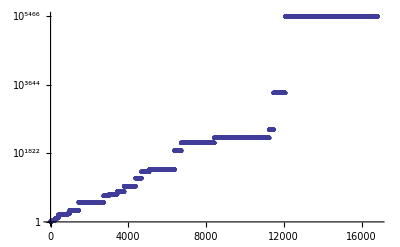

```mathematica
ListLogPlot[ReadList [FileNameForTupleBis[{3,31,43,173,229}]]]
```

```mathematica
N[Log[10,Last[ReadList [FileNameForTupleBis[{3,37,59,127,139}]]]]]
```

2903.89

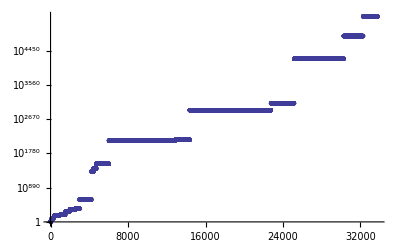

```mathematica
ListLogPlot[ReadList [FileNameForTupleBis[{3,37,59,127,139}]]]
```

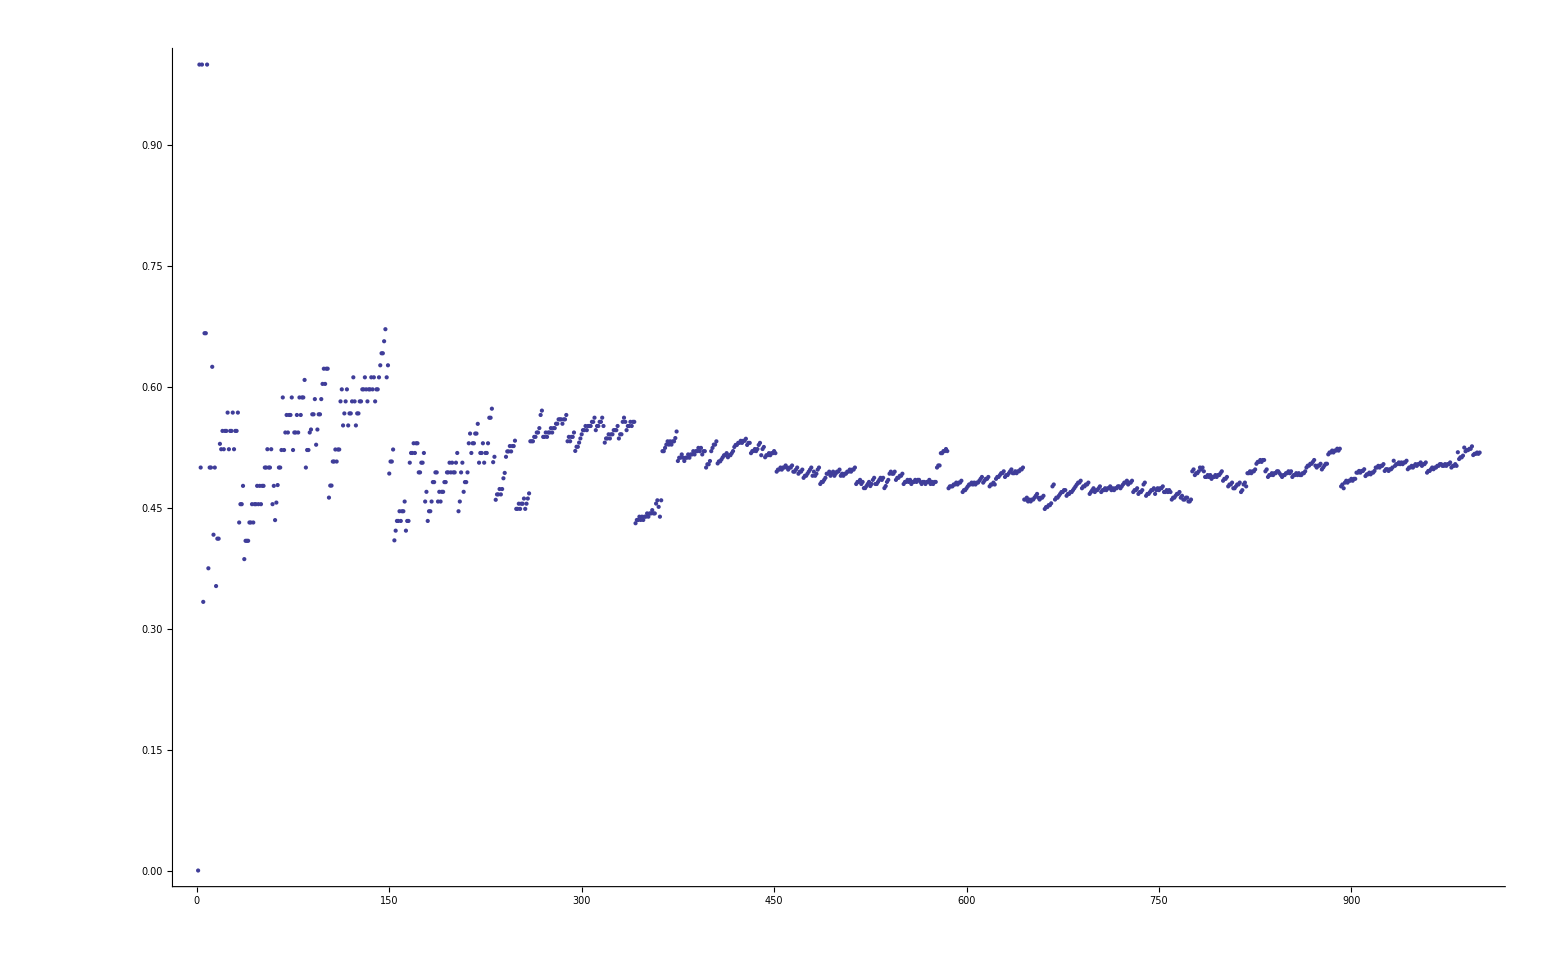

```mathematica
With[
{all=Take[ReadList [FileNameForTupleBis[{3,31,43,173,229}]],1000]},
ListPlot[Map[DigitRatio[IntegerDigits[#,3],1]&,all]]
]
```

```mathematica
DigitRatio [{10},1]
```

0

```mathematica
Last[ReadList [FileNameForTupleBis[{3,37,59,127,139}]]]
```

56232657862698998785789797483463034390744464320779595872930687841433175271191844088381058091020111206907817952609386521064272024273005269543311875773598828982237464239973610271847341202249452654739928029800229372629604608002975053519690785350756530308478360952167500981182513747893730635028768448720651211405007598723878121083954119502553713484800502166677105169266987177898378589255904900858648423849079332848625126685824050982200027727205984561917319197431512989129776467288017641355837602250399981068623955264324798631512586039557771932773377083443858235293190074110809758306499985191748754988007745248271414614451095638375274541808710747759452464663871832052194303405996023896595047457201898140055964646439597381015214800099104096188478488961671621566606608473557040810662607085169515750747637915662073563147006230024800870318757444852765681654489443297304327858648368585842948918903470997293721808624854059571834137430601702270020189008365400520246025105346769975189195692378115169365427655251305796309380341329593789831606110080147711943934142570186644673183931083152507342092131902389571126299476319667722324116928250011316803612697604832344935215076780954980480366472903459369429670015383805848188726743609371748114269723442469850510853655578783922217016619918593858373973219156517912575938230869355007